# GHZ STATES - NoiseModel IBM

## N = 5 Depolarizing channel

In this section the data refers to the measurement of qubit 0, with the parameter ϕ = (π j)/(n+1) that changes from 0 to (π (2n+1))/(n+1).

THEORY

```mathematica
n=5;
phi[j_]:=(Pi j)/(n+1)
S[ϕ_]:=1/2(1+Cos[n*ϕ])
Subscript[list, th]=Table[S[phi[j]],{j,0,(2*n+1)}];
N[Subscript[list, th]]
```

{1.,0.0669873,0.75,0.5,0.25,0.933013,0.,0.933013,0.25,0.5,0.75,0.0669873}

```mathematica
Subscript[x, axis]=Table[phi[j],{j,0,(2*n+1)}];
```

```mathematica
Length[Subscript[x, axis]]==Length[Subscript[list, th]]
```

True

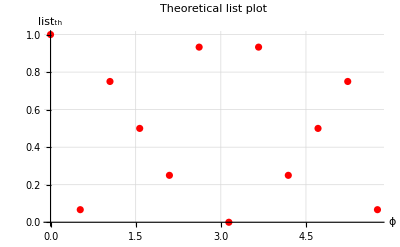

```mathematica
Subscript[listPlot, th]=ListPlot[Thread[{Subscript[x, axis],Subscript[list, th]}],AxesLabel->{HoldForm["ϕ"],HoldForm["list_th"]},PlotLabel->HoldForm["Theoretical list plot"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

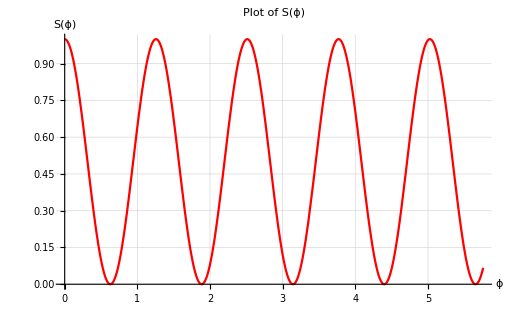

```mathematica
Subscript[plot, th]=Plot[S[ϕ],{ϕ,0,(Pi (2n+1))/(n+1)},AxesLabel->{HoldForm["ϕ"],HoldForm["S(ϕ)"]},PlotLabel->HoldForm["Plot of S(ϕ)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Red}]
```

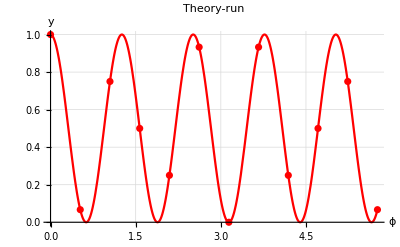

```mathematica
Show[Subscript[listPlot, th],Subscript[plot, th],AxesLabel->{HoldForm["ϕ"],HoldForm["y"]},PlotLabel->HoldForm["Theory-run"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, th]=Abs[N[Table[1/(2(n+1))*Sum[Exp[I  q phi[j]]*S[phi[j]],{j,0,(2*n+1)}],{q,-n,n}]]];
```

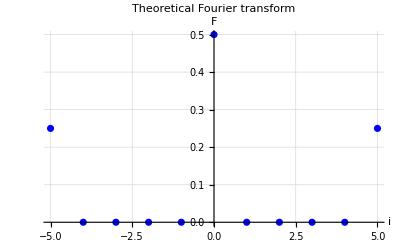

```mathematica
Subscript[FPlot, th]=ListPlot[Thread[{l,Subscript[F, th]}],AxesLabel->{HoldForm["i"],HoldForm["F"]},PlotLabel->HoldForm["Theoretical Fourier transform"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Blue}]
```

RUN NOISE MODEL

1000 shots

```mathematica
data1={1.0,0.06608333333333333,0.7510833333333333,0.4905833333333333,0.24866666666666665,0.9355,0.0,0.9284166666666667,0.24766666666666665,0.50475,0.75,0.06541666666666666}; (*γ=0.000125*)
data2={0.9046666666666666,0.08216666666666667,0.6905,0.46366666666666667,0.24625,0.8463333333333333,0.022,0.8484999999999999,0.2425,0.46249999999999997,0.6800833333333333,0.08366666666666667}; (*γ=0.00025*)
data3 = {0.81875,0.09433333333333332,0.6224166666666666,0.427,0.24241666666666667,0.7743333333333333,0.03866666666666667,0.76925,0.22741666666666666,0.4270833333333333,0.6311666666666667,0.09091666666666666};  (*γ=0.000375*)
data4={0.7428333333333333,0.10466666666666666,0.5801666666666666,0.38966666666666666,0.23199999999999998,0.7046666666666667,0.056999999999999995,0.7024166666666667,0.22466666666666665,0.39158333333333334,0.5675833333333333,0.10575};  (*γ=0.0005*)
data5={0.6739999999999999,0.10433333333333333,0.5255,0.3748333333333333,0.22325,0.6441666666666667,0.064,0.6298333333333334,0.22083333333333333,0.36791666666666667,0.5244166666666666,0.106};  (*γ=0.000625*)
data6 = {0.6164166666666666,0.11599999999999999,0.48316666666666663,0.34125,0.21616666666666665,0.5800833333333333,0.07675,0.5784166666666667,0.21225,0.355,0.48366666666666663,0.10958333333333332}; (*γ=0.00075*)
data7={0.56625,0.12141666666666666,0.45249999999999996,0.31975,0.21308333333333332,0.5304166666666666,0.0875,0.5280833333333333,0.21008333333333332,0.31866666666666665,0.4488333333333333,0.11891666666666666}; (*γ=0.000875*)
data8={0.5221666666666667,0.12075,0.40741666666666665,0.3065,0.19783333333333333,0.48774999999999996,0.09283333333333334,0.48541666666666666,0.19999999999999998,0.30016666666666664,0.40016666666666667,0.11958333333333333};  (*γ=0.001*)
data9={0.4795833333333333,0.12183333333333334,0.3738333333333333,0.27199999999999996,0.18816666666666665,0.44375,0.09416666666666666,0.44558333333333333,0.19025,0.2806666666666667,0.3755,0.12133333333333333};  (*γ=0.00225*)
data10={0.42824999999999996,0.11883333333333333,0.35283333333333333,0.26391666666666663,0.18766666666666665,0.4130833333333333,0.09616666666666666,0.4036666666666667,0.17891666666666667,0.26641666666666663,0.3475833333333333,0.12383333333333332};  (*γ=0.0035*)
data11={0.39349999999999996,0.11783333333333333,0.3153333333333333,0.24341666666666667,0.17683333333333331,0.3730833333333333,0.10533333333333333,0.37616666666666665,0.174,0.25075,0.322,0.11733333333333333};  (*γ=0.00475*)
data12={0.35841666666666666,0.12175,0.29466666666666663,0.23099999999999998,0.17116666666666666,0.32925,0.10325,0.3510833333333333,0.16891666666666666,0.23516666666666666,0.30491666666666667,0.11833333333333333};  (*γ=0.006*)
data13={0.3363333333333333,0.1235,0.27566666666666667,0.2215,0.16283333333333333,0.3175,0.10458333333333333,0.31575,0.15808333333333333,0.21958333333333332,0.27125,0.1235};  (*γ=0.001625*)
data14={0.3145,0.11424999999999999,0.2520833333333333,0.20516666666666666,0.15416666666666667,0.28741666666666665,0.10216666666666667,0.28933333333333333,0.15766666666666665,0.204,0.25325,0.11324999999999999};  (*γ=0.002875*)
data15={0.27508333333333335,0.11875,0.23741666666666666,0.191,0.15408333333333332,0.27016666666666667,0.10491666666666666,0.26641666666666663,0.148,0.19308333333333333,0.23066666666666666,0.11483333333333333};  (*γ=0.004125*)
data16={0.26466666666666666,0.12025,0.22083333333333333,0.17725,0.14766666666666667,0.24875,0.09866666666666667,0.24083333333333332,0.1455,0.17675,0.21958333333333332,0.11275};  (*γ=0.005375*)



data17={0.28783333333333333,0.12983333333333333,0.2585,0.215,0.16666666666666666,0.2886666666666667,0.111,0.2815,0.16699999999999998,0.22116666666666665,0.24683333333333332,0.12716666666666665};  (*γ=0.0013125*)
```

#### Plot of the data chosen

```mathematica
run=data1  (*inserire il data che si vuole*)
Length[run]
```

{1.,0.0660833,0.751083,0.490583,0.248667,0.9355,0.,0.928417,0.247667,0.50475,0.75,0.0654167}

12

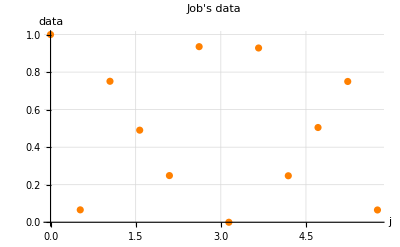

```mathematica
Subscript[plot, run]=ListPlot[Thread[{Subscript[x, axis],run}],AxesLabel->{HoldForm["j"],HoldForm["data"]},PlotLabel->HoldForm["Job's data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->Automatic, PlotLegends->{},PlotStyle->{Orange}]
```

#### DISCRETE FOURIER TRANSFORM

```mathematica
l=Table[i,{i,-n,n}];
```

```mathematica
Subscript[F, run]=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*run[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

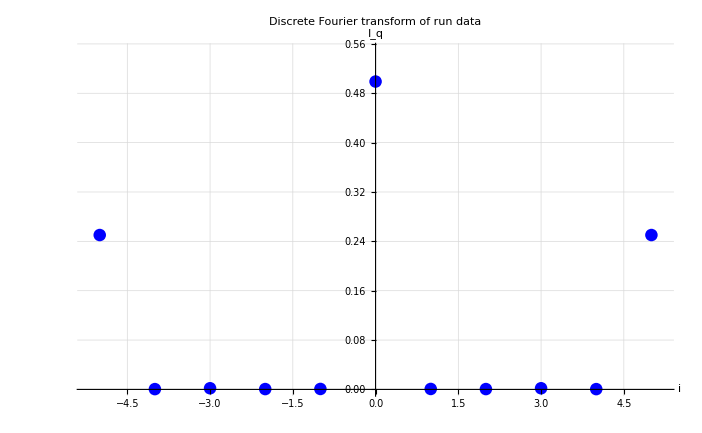

```mathematica
Subscript[I, run]=Subscript[FPlot, run]=ListPlot[Thread[{l,Subscript[F, run]}],AxesLabel->{HoldForm["i"],HoldForm["I_q"]},PlotLabel->HoldForm["Discrete Fourier transform of run data"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-n-0.2,n+0.2},{0,0.55}}, PlotLegends->{},PlotStyle->{Blue}]
```

Fidelity

```mathematica
F1=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data1[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F2=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data2[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F3=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data3[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F4=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data4[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F5=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data5[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F6=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data6[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F7=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data7[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F8=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data8[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F9=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data9[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F10=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data10[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F11=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data11[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F12=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data12[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F13=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data13[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F14=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data14[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F15=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data15[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F16=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data16[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
F17=Table[1/(2(n+1))*Abs[Sum[Exp[-I  q phi[j]]*data17[[j+1]],{j,0,(2*n+1)}]],{q,-n,n}];
```

```mathematica
F5Lower1= 2 √F1[[Length[F1]]];
F5Upper1=√(F1[[n+1]]/2)+√F1[[Length[F1]]];
F5Lower2= 2 √F2[[Length[F2]]];
F5Upper2=√(F2[[n+1]]/2)+√F2[[Length[F2]]];
F5Lower3= 2 √F3[[Length[F3]]];
F5Upper3=√(F3[[n+1]]/2)+√F3[[Length[F3]]];
F5Lower4= 2 √F4[[Length[F4]]];
F5Upper4=√(F4[[n+1]]/2)+√F4[[Length[F4]]];
F5Lower5= 2 √F5[[Length[F5]]];
F5Upper5=√(F5[[n+1]]/2)+√F5[[Length[F5]]];
F5Lower6= 2 √F6[[Length[F6]]];
F5Upper6=√(F6[[n+1]]/2)+√F6[[Length[F6]]];
F5Lower7= 2 √F7[[Length[F7]]];
F5Upper7=√(F7[[n+1]]/2)+√F7[[Length[F7]]];
F5Lower8= 2 √F8[[Length[F8]]];
F5Upper8=√(F8[[n+1]]/2)+√F8[[Length[F8]]];
F5Lower9= 2 √F9[[Length[F9]]];
F5Upper9=√(F9[[n+1]]/2)+√F9[[Length[F9]]];
F5Lower10= 2 √F10[[Length[F10]]];
F5Upper10=√(F10[[n+1]]/2)+√F10[[Length[F10]]];
F5Lower11= 2 √F11[[Length[F11]]];
F5Upper11=√(F11[[n+1]]/2)+√F11[[Length[F11]]];
F5Lower12= 2 √F12[[Length[F12]]];
F5Upper12=√(F12[[n+1]]/2)+√F12[[Length[F12]]];
F5Lower13= 2 √F13[[Length[F13]]];
F5Upper13=√(F13[[n+1]]/2)+√F13[[Length[F13]]];
F5Lower14= 2 √F14[[Length[F14]]];
F5Upper14=√(F14[[n+1]]/2)+√F14[[Length[F14]]];
F5Lower15= 2 √F15[[Length[F15]]];
F5Upper15=√(F15[[n+1]]/2)+√F15[[Length[F15]]];
F5Lower16= 2 √F16[[Length[F16]]];
F5Upper16=√(F16[[n+1]]/2)+√F16[[Length[F16]]];
F5Lower17= 2 √F17[[Length[F17]]];
F5Upper17=√(F17[[n+1]]/2)+√F17[[Length[F17]]];
```

Fidelity plot

```mathematica
V5Lower={F5Lower1,F5Lower2,F5Lower3,F5Lower4,F5Lower5,F5Lower6,F5Lower7,F5Lower8,F5Lower9,F5Lower10,F5Lower11,F5Lower12,F5Lower13,F5Lower14,F5Lower15,F5Lower16};
V5Upper={F5Upper1,F5Upper2,F5Upper3,F5Upper4,F5Upper5,F5Upper6,F5Upper7,F5Upper8,F5Upper9,F5Upper10,F5Upper11,F5Upper12,F5Upper13,F5Upper14,F5Upper15,F5Upper16};
gamma={0,0.002,0.004,0.006,0.008,0.01,0.012,0.014,0.016,0.018,0.02,0.022,0.024,0.026,0.028,0.03};
Lower=Thread[{gamma,V5Lower}];
Upper=Thread[{gamma,V5Upper}];
k=0.0305
retta=Plot[0.5,{x,0,k},PlotStyle->{Dashing[Tiny],Dashing[Large],Black}];
```

0.0305

```mathematica
verticalSize=430;
orSize=600;
```

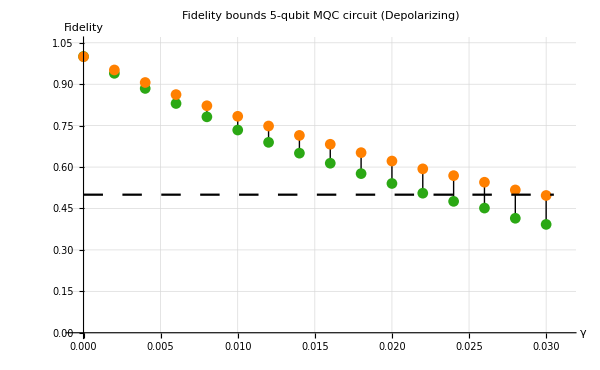

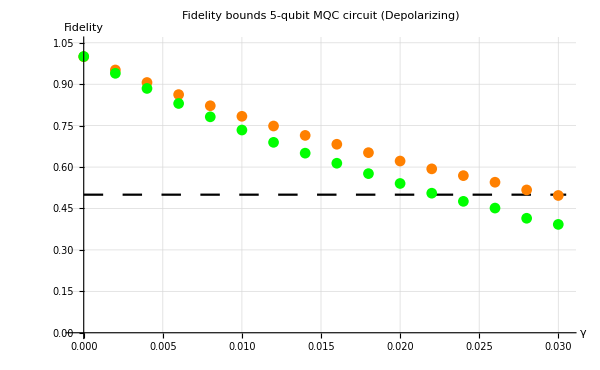

```mathematica
P5L=ListPlot[Lower,AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->16],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->16]},PlotLabel->HoldForm["Fidelity bounds 5-qubit MQC circuit (Depolarizing)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic , PlotRange->{{-0.0001,k},{0,1.05}}, PlotLegends->{},PlotStyle->{Green}];
P5U=ListPlot[Upper,AxesLabel->{HoldForm["γ"],HoldForm["Fidelity"]},PlotLabel->HoldForm["Fidelity bounds 5-qubit MQC circuit (Depolarizing)"],LabelStyle->{FontFamily->"Calibri",11,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Medium, GridLines->Automatic ,  PlotRange->{{-0.0005,k},{0,1.05}}, PlotLegends->{},PlotStyle->{Orange}];


salvare=ListPlot[{Thread[{gamma,V5Lower}],Thread[{gamma,V5Upper}]},Filling->{1->{2}},FillingStyle->{Black},PlotStyle->{RGBColor[0.17,0.66,0.08],Orange},AxesLabel->{Style["γ",Black,FontFamily->"HoldForm",FontSize->20],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->20]},PlotLabel->HoldForm["Fidelity bounds 5-qubit MQC circuit (Depolarizing)"],LabelStyle->{FontFamily->"Calibri",16,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Directive[18], GridLines->Automatic ,   PlotRange->{{-0.0005,k+0.0008},{0,1.05}}, PlotLegends->{},ImageSize->{orSize,verticalSize}];
Show[salvare,retta]

a=Show[retta,P5U,P5L,AxesLabel->{ Style["γ",Black,FontFamily->"HoldForm",FontSize->20],Style["Fidelity",Black,FontFamily->"HoldForm",FontSize->20]},PlotLabel->HoldForm["Fidelity bounds 5-qubit MQC circuit (Depolarizing)"],LabelStyle->{FontFamily->"Calibri",18,RGBColor[0.,0.,0.], Italic} , Ticks->Automatic ,TicksStyle->Directive[18], GridLines->Automatic ,  PlotRange->{{-0.0005,k},{0,1.05}}, PlotLegends->{},PlotStyle->{Orange},ImageSize->{orSize,verticalSize}]
```

```mathematica
parameter=0.022;
deltat=1;
T=(- deltat)/Log[1-parameter]
```

44.9527